## Исходные данные

```mathematica
(*xi≥0*)
InitF:=2*x1-4*x2+3;
InitL1:=3*x1≥8*x2;
InitL2:=2*x1+3*x2≤6;
InitL3:=x1-x2≤4;
InitL4:=-2*x1+x2≤2;
```

## Графический метод

Все ограничения заданы в виде неравенств, поэтому перейдём к уравнениям, введя дополнительные переменные.

```mathematica
L1:=3*x1-x3==8*x2;
L2:=2*x1+3*x2+x4==6;
L3:=x1-x2+x5==4;
L4:=-2*x1+x2+x6==2;
```

Общее число переменных равно 6, а число ограничений 4, следовательно задача имеет бесчисленное количество решений.
Задача решается в 2-мерном пространстве, поэтому её можно графически изобразить на плоскости.
В системе ограничений наибольшее число раз встречаются переменные x1 и x2, поэтому выберем их в качестве свободных.

### Используемые функции

Формирует из ограничений неравенства с учетом xi ≥ 0 (по условию).

```mathematica
FormInequalities:=Module[{a,b,c,d},
a=(x3/.Solve[L1,x3])[[1]]≥0;
b=(x4/.Solve[L2,x4])[[1]]≥0;
c=(x5/.Solve[L3,x5])[[1]]≥0;
d=(x6/.Solve[L4,x6])[[1]]≥0;
Return[{a,b,c,d}];
];
```

Формирует из ограничений неравенства с учетом xi ≤ 0 для наглядности построения.

```mathematica
FormInequalitiesInv:=Module[{a,b,c,d},
a=(x3/.Solve[L1,x3])[[1]]≤0;
b=(x4/.Solve[L2,x4])[[1]]≤0;
c=(x5/.Solve[L3,x5])[[1]]≤0;
d=(x6/.Solve[L4,x6])[[1]]≤0;
Return[{a,b,c,d}];
];
```

```mathematica
FormArea:=Module[{inEqs=FormInequalitiesInv, plot},
plot=RegionPlot[{inEqs},{x1,0,10},{x2,0,5},PlotLegends->{FormInequalities}, AxesLabel->Automatic, AspectRatio->Automatic];
Return[plot];
];
```

### Область допустимых значений

ОДР целевой функции представена белой областью.
Линии отклика представлены цветными параллельным линиями.

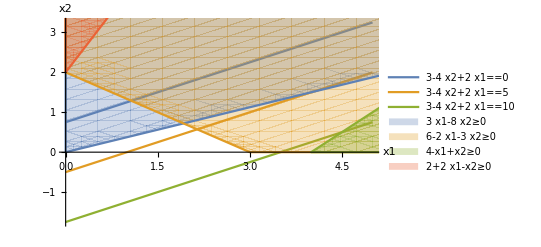

```mathematica
Module[{a,b,c,d,min,max},
OrigF[y_]:=x2/.Solve[InitF==y,x2];
Show[{Plot[{OrigF[0], OrigF[5], OrigF[10]},{x1,0,5},PlotLegends->{InitF==0,InitF==5,InitF==10}, PlotStyle->Thick,AxesLabel->{x1,x2}],FormArea}]
]
```

По линиям отклика видно, что целевая функция возрастает с увеличением x2 и уменьшением x1, что в ОДР соответствует значениям x1 = 3, x2 = 0.

```mathematica
Row[{"Fmax",Row[{Assuming[x1==3&&x2==0,Refine[InitF]],"(x1→3, x2→0)"},","]},"="]
```

==Fmax,,9(x1→3, x2→0)

## Симплекс-метод

```mathematica
Fs:=3-(-2*x1+4*x2);
L1s:=x3==0-(-3*x1+8*x2);
L2s:=x4==6-(2*x1+3*x2);
L3s:=x5==4-(1*x1-1*x2);
L4s:=x6==2-(-2*x1+1*x2);
```

Свободные члены во всех ограничения больше 0, следовательно ограничения совместны.

Все коэффициенты при свободных  переменных (x1, x2) разных знакову, поэтому условие оптимальности не выполняется.
Необходимо выбрать новую базисную переменную. В соответствии с правилом выбора свободной переменной в базис переводим переменную x1.
В соответствии с правилом выбора базисной переменной в свободные переменные переводим x3.

```mathematica
Fs:=3-(-4*x2/3-2*x3/3);
L1s:=x1==0-(8x2/3+x3/3);
L2s:=x4==6-(2*x1+3*x2);
L3s:=x5==4-(1*x1-1*x2);
L4s:=x6==2-(-2*x1+1*x2);
```

Все коэффициенты при свободных  переменных (x2, x3) отрицательные, что говорит о выполнении признака оптимальности для поиска минимума
Поэтому в свободные переменные переводим x4.

```mathematica
Fs:=9-(7x2+x4);
L1s:=x3==0-(-3*x1+8*x2);
L2s:=x1==3-(3*x2/2+x4/2);
L3s:=x5==4-(1*x1-1*x2);
L4s:=x6==2-(-2*x1+1*x2);
```

Теперь коэффициенты при всех свободных переменных (x2, x4) целевой функции положительные, выполняется условие оптимального решения
и целевая функция будет иметь максимальное значение.

```mathematica
Row[{"Fmax",Row[{Assuming[x2==0&&x4==0,Refine[FsMax]],"(x2→0, x4→0)"},","]},"="]
```

==Fmax,,9(x2→0, x4→0)